```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 179 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,VariationalMethods`,System`,Global`}

```mathematica
Clear[V]
V = (c x)/(x^2+a^2)
```

(c x)/(a^2+x^2)

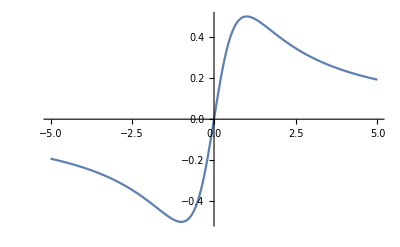

```mathematica
Plot[Evaluate[  V  //.  c -> 1  //.  a-> 1 ]  , { x, - 5, 5 } ]
```

```mathematica
Manipulate[
Plot[
Evaluate[( V //. c-> C //. a -> A )  ], { x , -5 , 5 } , PlotRange-> { -3,3} ]  , { C , -2 , 2 } , { A, -10 , 10 } ]
```

```mathematica
D[V, x]
```

-(2 c x^2)/((a^2+x^2)^2)+c/(a^2+x^2)

```mathematica
D[V, x] == 0
```

-(2 c x^2)/((a^2+x^2)^2)+c/(a^2+x^2)==0

```mathematica
Clear[xmin]
xmin = 
Flatten[Solve[ D[V, x] == 0  , x ]]
```

{x→-a,x→a}

```mathematica
D[D[V, x], x]
```

(8 c x^3)/((a^2+x^2)^3)-(6 c x)/((a^2+x^2)^2)

```mathematica
D[D[V, x], x] /. xmin[[1]]
```

c/(2 a^3)

```mathematica
D[D[V, x], x] /. xmin[[2]]
```

-c/(2 a^3)

```mathematica
Clear[transform]
transform = 
x[t] == -a + 𝓍[t]
```

x[t]==-a+𝓍[t]

```mathematica
Clear[xReplace]
xReplace = 
Flatten[Solve[ transform , x[t] ]] 

Clear[𝓍Replace]
𝓍Replace = 
Flatten[Solve[ transform , 𝓍[t] ] ]
```

{x[t]→-a+𝓍[t]}

{𝓍[t]→a+x[t]}

```mathematica
D[𝓍Replace, t]
```

{𝓍'[t]→x'[t]}

```mathematica
D[D[𝓍Replace, t], t]
```

{𝓍''[t]→x''[t]}

```mathematica
-D[V, x] /. x-> x[t] // Simplify
```

(c (-a^2+x[t]^2))/((a^2+x[t]^2)^2)

```mathematica
Clear[eomx]
eomx = 
m x''[t] == ( -D[V, x] /. x-> x[t] // Simplify  )
```

m x''[t]==(c (-a^2+x[t]^2))/((a^2+x[t]^2)^2)

```mathematica
xReplace
```

{x[t]→-a+𝓍[t]}

```mathematica
D[xReplace, t]
```

{x'[t]→𝓍'[t]}

```mathematica
D[D[xReplace, t], t]
```

{x''[t]→𝓍''[t]}

```mathematica
eomx
eomx /. xReplace 
eomx /. xReplace  /. D[D[xReplace, t], t]
```

m x''[t]==(c (-a^2+x[t]^2))/((a^2+x[t]^2)^2)

m x''[t]==(c (-a^2+(-a+𝓍[t])^2))/((a^2+(-a+𝓍[t])^2)^2)

m 𝓍''[t]==(c (-a^2+(-a+𝓍[t])^2))/((a^2+(-a+𝓍[t])^2)^2)

```mathematica
Clear[eom𝓍]
eom𝓍 = 
eomx /. xReplace  /. D[D[xReplace, t], t]
```

m 𝓍''[t]==(c (-a^2+(-a+𝓍[t])^2))/((a^2+(-a+𝓍[t])^2)^2)

```mathematica
eom𝓍[[2]] // ExpandNumerator // ExpandDenominator
```

(-2 a c 𝓍[t]+c 𝓍[t]^2)/(4 a^4-8 a^3 𝓍[t]+8 a^2 𝓍[t]^2-4 a 𝓍[t]^3+𝓍[t]^4)

```mathematica
(-2 a c 𝓍[t])/(4 a^4)
```

-(c 𝓍[t])/(2 a^3)

```mathematica
Clear[smallOsc]
smallOsc = 
m 𝓍''[t] == -(c 𝓍[t])/(2 a^3)
```

m 𝓍''[t]==-(c 𝓍[t])/(2 a^3)

```mathematica
Solve[ Coefficient[ Flatten[Solve[ smallOsc , 𝓍''[t] ]][[1,2]] , 𝓍[t] ] == - ω^2 , ω ][[2]]
```

{ω→(√c)/(√2 a^(3/2) √m)}